# ADAF outer boundary conditions

I want to evaluate the azimuthal component of the momentum equation, and check the value of j (the eigenvalue or "shooting parameter") and λ (the Mach number) for certain assumptions.

The idea is to understand better how to specify the outer boundary conditions (OBCs).

### Input parameters

```mathematica
alpha=0.3;
```

Mass in solar masses

```mathematica
m=1*^8;
```

```mathematica
beta=0.9;
```

Eigenvalue of the problem (shooting parameter)

```mathematica
j=3.5;
```

### Outer boundary conditions

Outer radius (in units of R_S)

```mathematica
(*rout=1.*^4;*)
```

Ion and electron temperatures in terms of the Virial temperature

```mathematica
Ti=0.6; Te=0.06;
```

You can specify the following OBC either as the Mach number or the outer angular velocity, both are equivalent.

```mathematica
omega=0.5*omegak;
```

### Physical constants and definitions

```mathematica
<<PhysicalConstants`
```

```mathematica
<<Units`
```

```mathematica
CGS[GravitationalConstant];
Level[%,1];
G=%[[1]]; (*this is to get rid of the units*)
```

```mathematica
k=CGS[BoltzmannConstant];
Level[%,1];
k=%[[1]];
```

```mathematica
mH=CGS[ProtonMass];
Level[%,1];
mH=%[[1]];
```

```mathematica
c=CGS[SpeedOfLight];
Level[%,1];
c=%[[1]];
```

Solar mass in g

```mathematica
solarmass=1.99*^33;
```

```mathematica
M=m*solarmass;
```

Mean molecular weights

```mathematica
mui=1.23; mue=1.14;
```

Schwarzschild radius

```mathematica
Rs=2*G*M/c^2;
```

```mathematica
R=rout*Rs;
```

Virial temperature

```mathematica
Tv=3.6*^12*(Rs/R)
Ti=Ti*Tv;
Te=Te*Tv;
```

(3.6×10^12)/rout

## Equations

Keplerian angular velocity:

```mathematica
omegak=Sqrt[G*M/R^3]
```

0.00071737 √(1/rout^3)

Isothermal sound speed:

```mathematica
cs=Sqrt[k/(beta*mH)*(Ti/mui+Te/mue)]
```

1.33581×10^10 √(1/rout)

```mathematica
lambda=-alpha*R*cs/(omega*R^2-j)
```

-(1.18421×10^23)/(√(1/rout) (-3.5+3.13212×10^23 √(1/rout^3) rout^2))

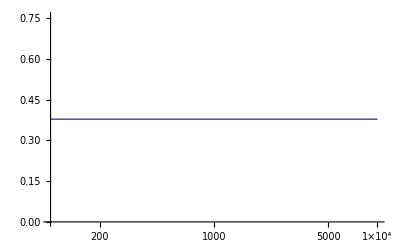

```mathematica
LogLinearPlot[-lambda,{rout,100,1*^4}]
```